## Отчёт по 5 лабараторной работе -Graphics-

```mathematica
(*А)*)
(*Определение функции f(x)*)
f[x_]:=Tan[Log[3 x]]

(*Точка x0, где нужно найти производные*)
x0=7.17;

D[f[x],x]
```

Sec[Log[3 x]]^2/x

```mathematica
D[f[x],{x,2}]
```

-Sec[Log[3 x]]^2/x^2+(2 Sec[Log[3 x]]^2 Tan[Log[3 x]])/x^2

```mathematica
(*Производная первого порядка в точке*)
```

```mathematica
d11=D[f[x],x]/. x->x0
```

0.140217

```mathematica
(*Производная второго порядка в точке*)
```

```mathematica
d21=D[f[x],{x,2}]/. x->x0
```

-0.0224193

```mathematica
(*Б)*)
(*Задаём шаг*)
h=0.1;

(*Сетка четырёх значений y[i] на интервале[x0-h,x0+3h]*)
y=Table[f[x0+i h],{i,-1,3}]; (*x[-1] до x[3]*)

(*Вычисляем конечные разности*)
Δy=Table[y[[i+1]]-y[[i]],{i,1,Length[y]-1}]; (*Первая разность*)
Δ2y=Table[Δy[[i+1]]-Δy[[i]],{i,1,Length[Δy]-1}]; (*Вторая разность*)
Δ3y=Table[Δ2y[[i+1]]-Δ2y[[i]],{i,1,Length[Δ2y]-1}]; (*Третья разность*)

(*Формулы для производных*)
pr1=(Δy[[2]]-1/2 Δ2y[[1]]+1/3 Δ3y[[1]])/h (*Subscript[y, i]^,*)
pr2=(Δ2y[[1]]-Δ3y[[1]])/h^2 (*Subscript[y, i]^(,,)*)
```

0.140277

-0.0236073

```mathematica
(*Абсолютная погрешность*)
{Abs[d11-pr1],Abs[d21-pr2]}
```

{0.0000597097,0.00118799}

```mathematica
Δy
Δ2y
Δ3y
```

{0.0141359,0.0139116,0.0136992,0.0134978}

{-0.00022426,-0.000212447,-0.000201367}

{0.0000118133,0.0000110799}

```mathematica
(*Задаём шаг*)
h=0.01;

(*Сетка значений y[i] на интервале[x0-h,x0+3h]*)
y=Table[f[x0+i h],{i,-1,3}]; (*x[-1] до x[3]*)

(*Вычисляем конечные разности*)
Δy=Table[y[[i+1]]-y[[i]],{i,1,Length[y]-1}]; (*Первая разность*)
Δ2y=Table[Δy[[i+1]]-Δy[[i]],{i,1,Length[Δy]-1}]; (*Вторая разность*)
Δ3y=Table[Δ2y[[i+1]]-Δ2y[[i]],{i,1,Length[Δ2y]-1}]; (*Третья разность*)

(*Формулы для производных*)
pr1=(Δy[[2]]-1/2 Δ2y[[1]]+1/3 Δ3y[[1]])/h (*Subscript[y, i]^,*)
pr2=(Δ2y[[1]]-Δ3y[[1]])/h^2 (*Subscript[y, i]^(,,)*)
```

0.140218

-0.022541

```mathematica
(*Абсолютная погрешность*)
{Abs[d11-pr1],Abs[d21-pr2]}
```

{6.08459×10^-7,0.000121626}

```mathematica
(*Сравнение результатов численного дифференцирования для шагов
  ℎ1=0.1 и ℎ2=0.01 показывает, что уменьшение шага приводит к 
 уменьшению погрешности вычисления.*)
```

-Graphics-

```mathematica
(*22222222222222222222*)
(*Провекри трижды дефферинцирования*)
```

```mathematica
(*Функция трижды дифференцируема*)
f[x_]:=Sinh[Log[Cosh[x]]];
```

```mathematica
D[f[x],{x,3}]
```

4 Sinh[x]-3/2 Sech[x] (2 Cosh[x]^2+2 Sinh[x]^2) Tanh[x]+3 Cosh[x] Sinh[x] (-Sech[x]^3+Sech[x] Tanh[x]^2)+1/2 (-1+Cosh[x]^2) (5 Sech[x]^3 Tanh[x]-Sech[x] Tanh[x]^3)

```mathematica
a=-1;b=3;h=0.2;dataPr=N[Table[{a+i*h,(f[a+(i+1)*h]-f[a+(i-1)*h])/(2*h)},{i,0,20}]]
```

{{-1.,-0.835793},{-0.8,-0.69139},{-0.6,-0.542088},{-0.4,-0.37772},{-0.2,-0.195081},{0.,0.},{0.2,0.195081},{0.4,0.37772},{0.6,0.542088},{0.8,0.69139},{1.,0.835793},{1.2,0.988688},{1.4,1.1639},{1.6,1.37461},{1.8,1.63363},{2.,1.95415},{2.2,2.35075},{2.4,2.84035},{2.6,3.44321},{2.8,4.18383},{3.,5.09213}}

```mathematica
a=-1;b=3;h=0.2;
```

```mathematica
(*Формула второго порядка точности*)
fPrime[x_]:=(f[x+h]-f[x-h])/(2 h)

(*Генерация таблицы приближённых значений
производных на отрезке от-1 до 3 с шагом 0.2*)
table=Table[{x,fPrime[x]},{x,-1,3,0.2}];
TableForm[table]
```

-1. | -0.835793
-0.8 | -0.69139
-0.6 | -0.542088
-0.4 | -0.37772
-0.2 | -0.195081
0. | 0.
0.2 | 0.195081
0.4 | 0.37772
0.6 | 0.542088
0.8 | 0.69139
1. | 0.835793
1.2 | 0.988688
1.4 | 1.1639
1.6 | 1.37461
1.8 | 1.63363
2. | 1.95415
2.2 | 2.35075
2.4 | 2.84035
2.6 | 3.44321
2.8 | 4.18383
3. | 5.09213

```mathematica
(*Функция трижды дифференцируема*)
f[x_]:=Sinh[Log[Cosh[x]]];
```

```mathematica
(*Вычисление производной функции с помощью D*)
pr[x_]:=D[f[x],x]

(*Генерация точек для приближенной производной*)
points=Table[{x,fPrime[x]},{x,-1,3,0.2}];
```

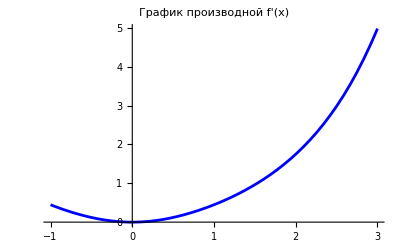

```mathematica
Plot[f[x],{x,-1,3},PlotStyle->Blue,PlotLabel->"График производной f'(x)"]
```

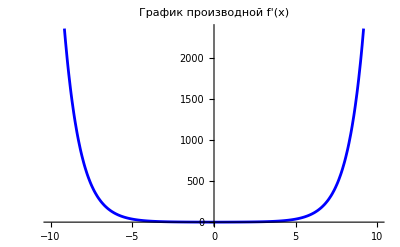

```mathematica
Plot[f[x],{x,-10,10},PlotStyle->Blue,PlotLabel->"График производной f'(x)"]

(*Пример функции*)
```

```mathematica
f[x_]:=Sinh[Log[Cosh[x]]];
Plot[f[x],{x,-1,3},PlotStyle->Blue,PlotLabel->"График производной f'(x)"]
```

-Graphics-

```mathematica
(*Вычисление аналитической производной*)
fPrime[x_]=D[f[x],x]
```

Sinh[x]-1/2 (-1+Cosh[x]^2) Sech[x] Tanh[x]

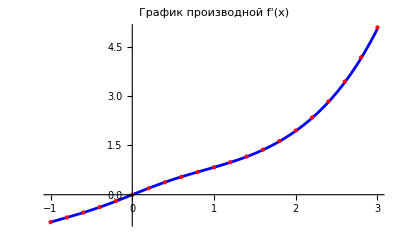

```mathematica
Show[Plot[fPrime[x],{x,-1,3},PlotStyle->Blue,PlotLabel->"График производной f'(x)"],ListPlot[table,PlotStyle->{Red,PointSize[Medium]},PlotLabel->"Приближенные значения"]]
```

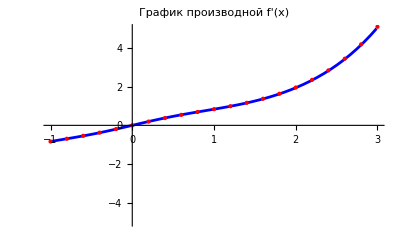

```mathematica
Show[Plot[fPrime[x],{x,-1,3},PlotStyle->Blue,PlotLabel->"График производной f'(x)",PlotRange->{Automatic,{-5,5}}],ListPlot[table,PlotStyle->{Red,PointSize[Medium]},PlotLabel->"Приближенные значения"]]
```

-Graphics-

```mathematica
(*Вычисление аналитической производной*)
fPrime[x_]=D[f[x],x]

(*Параметры задачи*)
a=-1;b=3;h=0.2;
xi=Range[a,b,h]; (*Узлы сетки*)

(*Вычисление приближенных значений производной ЕСТЬ ВЫШЕ*)
centralDiff[x_]:=(f[x+h]-f[x-h])/(2 h)

(*Вычисление точных значений производной на узлах сетки*)
exactDerivatives=fPrime[xi];

(*Вычисление приближенных значений на узлах сетки*)
approxDerivatives2=Table[centralDiff[x],{x,xi[[2;;-2]]}];
approxDerivatives2=Prepend[approxDerivatives2,(f[xi[[2]]]-f[xi[[1]]])/h]; (*Левая разность*)
approxDerivatives2=Append[approxDerivatives2,(f[xi[[-1]]]-f[xi[[-2]]])/h]; (*Правая разность*)
Print["xi = ",xi];
Print["exactDerivatives = ",exactDerivatives];
Print["approxDerivatives = ",approxDerivatives2];
```

f'[x]

xi = {-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.}

exactDerivatives = f'[{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.}]

approxDerivatives = {5. (-f[-1.]+f[-0.8]),2.5 (-f[-1.]+f[-0.6]),2.5 (-f[-0.8]+f[-0.4]),2.5 (-f[-0.6]+f[-0.2]),2.5 (-f[-0.4]+f[5.55112×10^-17]),2.5 (-f[-0.2]+f[0.2]),2.5 (-f[1.66533×10^-16]+f[0.4]),2.5 (-f[0.2]+f[0.6]),2.5 (-f[0.4]+f[0.8]),2.5 (-f[0.6]+f[1.]),2.5 (-f[0.8]+f[1.2]),2.5 (-f[1.]+f[1.4]),2.5 (-f[1.2]+f[1.6]),2.5 (-f[1.4]+f[1.8]),2.5 (-f[1.6]+f[2.]),2.5 (-f[1.8]+f[2.2]),2.5 (-f[2.]+f[2.4]),2.5 (-f[2.2]+f[2.6]),2.5 (-f[2.4]+f[2.8]),2.5 (-f[2.6]+f[3.]),5. (-f[2.8]+f[3.])}

```mathematica
Sinh[x]-1/2 (-1+Cosh[x]^2) Sech[x] Tanh[x]
```

Sinh[x]-1/2 (-1+Cosh[x]^2) Sech[x] Tanh[x]

```mathematica
int2=h2*Sum[f[(a+(i-1)*h2+(a+i*h2))/2],{i,1,n2}]
```

h2 ∑_(i=1)^n2 f[1/2 (-2+h2 (-1+i)+h2 i)]

```mathematica
(*33333333333333TrapInt2=(h2/2)*(f[a]+f[b]+2*Sum[f[a+i*h2],{i,1,n2-1}])333333333333333333333333333*)
```

```mathematica
f[x_]:=((x^2+6)^(1/3))/(3x+√(x^2+0.6));
```

```mathematica
(*а)Формула средних прямоугольников*)
```

```mathematica
(*Интервал интегрирования*)
a=0.7; b=1.5;
```

```mathematica
n1=8;
h1=(b-a)/n1;
X1=N[Table[(a+i*h1)+h1/2,{i,0,n1-1}]];
int1=(b-a)/n1*∑_(i=1)^n1 f[X1[[i]]]
```

0.343792

```mathematica
n2=10;
h2=(b-a)/n2;
X2=N[Table[(a+i*h2)+h2/2,{i,0,n2-1}]];
int2=(b-a)/n2*∑_(i=1)^n2 f[X2[[i]]]
```

0.343864

```mathematica
Richardson=int1+(n1^2/(n2^2-n1^2)*(int2-int1))
```

0.34392

```mathematica
(*Б)Метод трапеций*)

TrapInt1=(h1/2)*(f[a]+f[b]+2*Sum[f[a+i*h1],{i,1,n1-1}])
TrapInt2=(h2/2)*(f[a]+f[b]+2*Sum[f[a+i*h2],{i,1,n2-1}])
TrapIntRichardson=TrapInt1+(n1^2/(n2^2-n1^2)*(TrapInt2-TrapInt1))
```

0.344396

0.344251

0.344138

```mathematica
-Graphics-

(*4444444444444444444444444444444444444444*)
```

```mathematica
(*Табличные данные*)
x={1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9, 2.0,2.1, 2.2,2.3,2.4,2.5,2.6,2.7,2.8};
y={0.1823,0.2624,0.3365,0.4055,0.4700,0.5306,0.5878,
0.6419,0.6931,0.7419,0.8329,0.8755,0.9163,0.9555,0.9933,0.9933,1.0296};
```

```mathematica
(*Данные для n=8*)
x8=x[[1;; ;;2]]
y8=y[[1;; ;;2]]
```

{1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8}

{0.1823,0.3365,0.47,0.5878,0.6931,0.8329,0.9163,0.9933,1.0296}

```mathematica
(*Данные для n=16*)
x16=x;
y16=y;
```

```mathematica
SimpsonRule[x_,y_]:=Module[{n,h,oddSum,evenSum},n=Length[x]-1;
h=(x[[-1]]-x[[1]])/n;
oddSum=Total[y[[2;;-1;;2]]];
evenSum=Total[y[[3;;-2;;2]]];
(h/3) (y[[1]]+y[[-1]]+4 oddSum+2 evenSum)];

(*Вычисления для n=8 и n=16*)
I8=SimpsonRule[x8,y8]
I16=SimpsonRule[x16,y16]
```

1.09151

1.08327

```mathematica
(*555555555555555555555*)
-Graphics-
```

```mathematica
f[x_]:=Log[2x]/(4x+1);
a=1.1; b=2;
```

```mathematica
(*Узлы квадратурной формулы Гаусса 
соответствуют корням полинома Лежандра*)
```

```mathematica
LegendreP[7,t]
```

1/16 (-35 t+315 t^3-693 t^5+429 t^7)

```mathematica
sl=NSolve[LegendreP[7,t]== 0,t]
```

{{t→-0.949108},{t→-0.741531},{t→-0.405845},{t→0.},{t→0.405845},{t→0.741531},{t→0.949108}}

```mathematica
tt=t/.sl
```

{-0.949108,-0.741531,-0.405845,0.,0.405845,0.741531,0.949108}

```mathematica
(*Матрица моментов для нахождения весов*)
```

```mathematica
T=Table[If[i==1,1,(tt[[j]])^(i-1)],{i,7},{j,7}];
MatrixForm[T]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
-0.949108 | -0.741531 | -0.405845 | 0. | 0.405845 | 0.741531 | 0.949108
0.900806 | 0.549868 | 0.16471 | 0. | 0.16471 | 0.549868 | 0.900806
-0.854962 | -0.407745 | -0.0668469 | 0. | 0.0668469 | 0.407745 | 0.854962
0.811451 | 0.302355 | 0.0271295 | 0. | 0.0271295 | 0.302355 | 0.811451
-0.770155 | -0.224206 | -0.0110104 | 0. | 0.0110104 | 0.224206 | 0.770155
0.73096 | 0.166256 | 0.0044685 | 0. | 0.0044685 | 0.166256 | 0.73096)

```mathematica
(*Правая часть линейной системы содержит коэффициенты
 разложения в базис полиномов Лежандра*)
```

```mathematica
B=Table[If[EvenQ[i]==True,0,2/i],{i,7}]//N
```

{2.,0.,0.666667,0.,0.4,0.,0.285714}

```mathematica
(*Решается система 𝑇⋅A=B*)
```

```mathematica
A=LinearSolve[T,B]
```

{0.129485,0.279705,0.38183,0.417959,0.38183,0.279705,0.129485}

```mathematica
(*Итоговая формула квадратурной формулы Гаусса*)
```

```mathematica
int=(b-a)/2*∑_(i=1)^7 A[[i]]*f[(b+a)/2+(b-a)/2*tt[[i]]]
```

0.139416